## Definitions

```mathematica
tprec=40;(* target precision for interpolated Fm *)
prec=10*tprec; (* precision for interpolation should be sufficient to get at least 16 digits *)
nintervals=7; (* # of intervals to subdivide [0,1] into *)
delta=1/nintervals; (* step size *)
order=7; (* polynomial order *)
mmax=40;

(* to determine Tmax needed to guarantee full relative precision, must solve *)
doubleEpsilon=10^(-16);
FindRoot[T^(mmax-1/2)*Exp[-T]==doubleEpsilon*Gamma[mmax+1/2],{T,60},WorkingPrecision->50];
Tmax=Ceiling[T/.%];
Print["will compute up to T=",Tmax," to ensure relative precision of ",N[doubleEpsilon]];
```

will compute up to T=117 to ensure relative precision of 1.×10^-16

## Evaluate Boys function in analytic form to guarantee precision

This takes ~150 seconds on a 2017 MacBook Pro ... grab a quick coffee

```mathematica
Fm[m_,T_]:=Module[{t},Return[Integrate[t^(2 m) Exp[-T t^2],{t,0,1}]]];
timer=Timing[Table[Fm[m,T],{m,0,mmax}]];
Print["Tabulated Boys function up to m=",mmax," in ",timer[[1]]," seconds"];
FmTable=timer[[2]];
```

Tabulated Boys function up to m=40 in 147.069 seconds

## Interpolate

### basic formulas

```mathematica
(* roots of Chebyshev polynomial on interval [-1/2,1/2] *)
chebnodes[n_]:=Table[Cos[(2k-1)π/(2n)]/2 ,{k,1,n}]; 
(* coefficients of the interpolating polynomial P_n[y], where y=(x-(b+a)/2)/(b-a), for Fm[x] on [a,b] *)
chebcoeffs[a_,b_,n_,m_]:=Module[{x,f,A,c,cc,nnodes,y},
nnodes=n+1;
x=chebnodes[nnodes];
f=Table[N[FmTable[[m+1]]/.T->((b-a)x[[k]]+(b+a)/2),50],{k,1,nnodes}];
(* evaluate Chebyshev polynomoials at the nodes *)
A=Table[ChebyshevT[ord,x[[k]]],{k,1,nnodes},{ord,0,n}];
cc=LinearSolve[A,f];
c=CoefficientList[Sum[cc[[ord+1]]ChebyshevT[ord,y],{ord,0,n}],y];
(* this loses precision badly:
c=CoefficientList[Expand[Sum[f[[i]]Product[If[i==j,1,(y-x[[j]])/(x[[i]]-x[[j]])],{j,1,nnodes}],{i,1,nnodes}]],y];*)
Return[c]
];
(* Lagrange interpolating polynomial *)
Pn[x_,c_,a_,b_]:=Module[{y},y=(x-(b+a)/2)/(b-a);Return[Sum[c[[i]]If[i==1,1,y^(i-1)],{i,1,Length[c]}]]
];
```

### OK, let’s do it

This will take awhile ... go get lunch

```mathematica
ToCString[x_]:=ToString[CForm[x]];

ofile=OpenWrite["boys_cheb"<>ToString[order]<>".h"];
WriteLine[ofile, "#ifndef LIBINT2_STATICS_INITIALIZATION"];
WriteLine[ofile,"static constexpr const std::size_t interpolation_order="<>ToCString[order]<>";"];
WriteLine[ofile,"static constexpr const double cheb_table_tmax="<>ToCString[Tmax]<>";"];
WriteLine[ofile,"static constexpr const double cheb_table_delta="<>ToCString[delta]<>";"];
WriteLine[ofile,"static constexpr const std::size_t cheb_table_mmax="<>ToCString[mmax]<>";"];
WriteLine[ofile,"static constexpr const std::size_t cheb_table_nintervals="<>ToCString[Tmax*nintervals]<>";"];
WriteLine[ofile, "#if LIBINT2_CONSTEXPR_STATICS"];
WriteLine[ofile, "static constexpr double cheb_table[cheb_table_nintervals][(cheb_table_mmax+1)*(interpolation_order+1)]="];
WriteLine[ofile, "#else"];
WriteLine[ofile, "static double cheb_table[cheb_table_nintervals][(cheb_table_mmax+1)*(interpolation_order+1)];"];
WriteLine[ofile, "#endif"];
WriteLine[ofile, "#else"];
WriteLine[ofile, "template<> double libint2::FmEval_Chebyshev"<>ToCString[order]<>"<double>::cheb_table[cheb_table_nintervals][(cheb_table_mmax+1)*(interpolation_order+1)]="];
WriteLine[ofile, "#endif"];
WriteLine[ofile,"#if defined(LIBINT2_STATICS_INITIALIZATION) || LIBINT2_CONSTEXPR_STATICS"];
WriteLine[ofile,"{"];

tabmaxabserror=0;
tabmaxrelerror=0;
Do[
WriteLine[ofile,If[t==0,"",","]<>"{"];
Do[
a=N[t*delta,prec];
b=N[(t+1)*delta,prec];
c=chebcoeffs[a,b,order,m];
refvalues=Table[Block[{$MaxExtraPrecision=1000},N[Limit[FmTable[[m+1]],T->x],tprec]],{x,a,b,delta/20}];
values=Table[Pn[N[x,tprec],c,a,b],{x,a,b,delta/20}];
abserror=Table[Abs[refvalues[[i]]-values[[i]]],{i,Length[refvalues]}];
relerror=Table[abserror[[i]]/Abs[refvalues[[i]]],{i,Length[refvalues]}];
maxabserror=Max[abserror];
maxrelerror=Max[relerror];
tabmaxabserror=Max[maxabserror,tabmaxabserror];
tabmaxrelerror=Max[maxrelerror,tabmaxrelerror];
WriteLine[ofile,"// ["<>ToCString[N[a,5]]<>","<>ToCString[N[b,5]]<>"]: m="<>ToCString[m]<>" maxabserror="<>ToCString[maxabserror]<>" maxrelerror="<>ToCString[maxrelerror]];
Do[
WriteLine[ofile,ToCString[N[c[[i+1]],tprec]]<>If[i==order&&m==mmax,"",","]],
{i,0,order}];
,{m,0,mmax}];
WriteLine[ofile,"}"];
,
{t,0,nintervals*Tmax-1}];
WriteLine[ofile,"};"];
WriteLine[ofile, "#endif"];
WriteLine[ofile, "#ifndef LIBINT2_STATICS_INITIALIZATION"];
WriteLine[ofile,"const double cheb_table_maxrelerror="<>ToCString[tabmaxrelerror]<>";"];
WriteLine[ofile,"const double cheb_table_maxabserror="<>ToCString[tabmaxabserror]<>";"];
WriteLine[ofile, "#endif"];
Close[ofile];
```

### This plots the error ... Chebyshev nodes are indeed near ideal

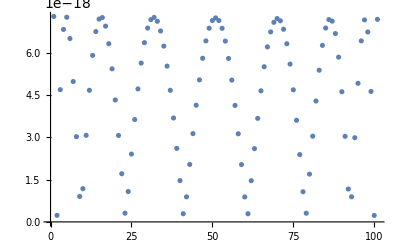

```mathematica
cc=chebcoeffs[N[0,prec],N[1/nintervals,prec],order,0];
ListPlot[Table[Abs[N[Fm[0,x],prec]-Pn[x,cc,0,1/nintervals]],{x,0,1/nintervals,1/(100*nintervals)}]]
```